```mathematica
(*Author: Oleg Kravchenko, 
Date: 11/09/15; 
Upd.01: 23/01/16*)
```

```mathematica
ClearAll["Global`*"]
```

### CIP - BS plots; Ref: NIFS-778, Basis Set Approach in the Constrained Interpolation Profile Method, T. Utsumi, J. Koga, T. Yabe, Y. Ogata, E. Matsunaga, T. Aoki and M. Sekine, July 2003

### Parameters;

```mathematica
ImgSz=250;
```

### Basic Functions;

```mathematica
BasisCIPBS[x_,k_,K_]:=Module[{ϕList,ϕL,ϕR,ϕ},
ϕK[x,K]:=Sum[Subscript[a, i] x^i,{i,0,2K+1,1}];
EqnSysL[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->-h)==0,{l,0,K,1}]
}//Flatten;
EqnSysR[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->h)==0,{l,0,K,1}]
}//Flatten;
ϕList={
ϕL=ϕK[x,K]/.Solve[EqnSysL[k,K],CoefficientList[ϕK[x,K],x]] ,
ϕR=ϕK[x,K]/.Solve[EqnSysR[k,K],CoefficientList[ϕK[x,K],x]],
(*ϕ=ϕL θ[x+1]+ϕR θ[x]*)
ϕ=Piecewise[{
{ϕL[[1]],-h≤x≤0},
{ϕR[[1]],0≤x≤h}
}]
}//Flatten
]
```

#### Interpolation;

True

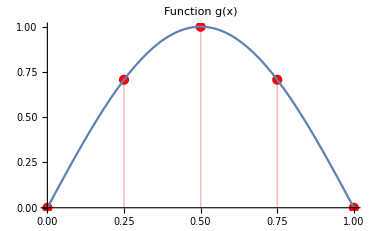
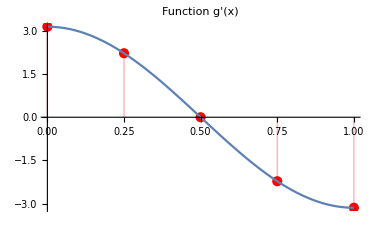
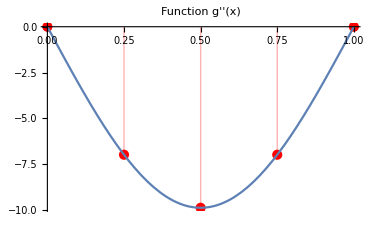

```mathematica
(*Function to be interpolated*)
gFunc[x_]:=Sin[π x]
ya[x_]:=-1/π^2 gFunc[x]
(*gFunc[x_]:=6 (1-x) x-6 x^2
ya[x_]:=x^3(1-x)*)

D[ya[x],{x,2}]==gFunc[x]

d1ya[x_]:=D[ya[x],x]//Evaluate
g1Func[x_]:=(0x+D[gFunc[x],{x,1}])//Evaluate
g2Func[x_]:=(0x +D[gFunc[x],{x,2}])//Evaluate
g3Func[x_]:=(0x +D[gFunc[x],{x,3}])//Evaluate
(*Parameters*)
a=0;
b=1;
nx=5;
hx=(b-a)/(nx-1);
(*Arrays*)
xTbl=Table[a+k*hx,{k,0,nx-1,1}]//N;
g0Tbl=gFunc@xTbl;
g1Tbl=g1Func@xTbl;
g2Tbl=g2Func@xTbl;
g3Tbl=g3Func@xTbl;
yaTbl=ya@xTbl;
d1yaTbl=d1ya@xTbl;

Row[{Show[{ListPlot[Partition[Riffle[xTbl,g0Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g(x)",PlotLegends->gFunc[x]],
Plot[gFunc[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant",PlotRange->All]}],Show[{ListPlot[Partition[Riffle[xTbl,g1Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g'(x)",PlotLegends->g1Func[x]],
Plot[g1Func[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant"]}],
Show[{ListPlot[Partition[Riffle[xTbl,g2Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g''(x)",PlotLegends->g2Func[x]],
Plot[g2Func[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant"]}]
}]
```

```mathematica
yaTbl
g0Tbl
g1Tbl
g2Tbl
d1yaTbl
```

{0.,-0.0716449,-0.101321,-0.0716449,-1.24083×10^-17}

{0.,0.707107,1.,0.707107,1.22465×10^-16}

{3.14159,2.22144,1.92367×10^-16,-2.22144,-3.14159}

{0.,-6.97886,-9.8696,-6.97886,-1.20868×10^-15}

{-0.31831,-0.225079,-1.94909×10^-17,0.225079,0.31831}

#### CIP-BS^1;

```mathematica
Clear[n,g0,g1,rhs,lhs,lhs01,lhs02,rhs01,rhs02]
(*lhs01[n_]:=6/(5 h)Subscript[f0, n-1]+ 1/10 Subscript[f1, n-1]-12/(5 h)Subscript[f0, n]+0 Subscript[f1, n] +6/(5 h)Subscript[f0, n+1]-1/10 Subscript[f1, n+1];
rhs01[n_]:=(9 h)/70 Subscript[g0, n-1]+(13 h^2)/420 Subscript[g1, n-1]+(26 h)/35 Subscript[g0, n]+0 Subscript[g1, n]+(9 h)/70 Subscript[g0, n+1]-(13 h^2)/420 Subscript[g1, n+1];
lhs02[n_]:=-1/10 Subscript[f0, n-1]+h/30 Subscript[f1, n-1]+0 Subscript[f0, n]-(4 h)/15 Subscript[f1, n]+1/10 Subscript[f0, n+1]+h/30 Subscript[f1, n+1];
rhs02[n_]:=(-13 h^2)/420 Subscript[g0, n-1]-h^3/140 Subscript[g1, n-1]+0 Subscript[g0, n]+(2 h^3)/105 Subscript[g1, n]+(13 h^2)/420 Subscript[g0, n+1]-h^3/140 Subscript[g1, n+1];

Column[{
(lhs01[2]/.Subscript[f0, 1]->0/.Subscript[f1, 1]->0)==rhs01[2],
lhs01[3]==rhs01[3],
(lhs01[4]/.Subscript[f0, 5]->0/.Subscript[f1, 5]->0)==rhs01[4],
(lhs02[2]/.Subscript[f0, 1]->0/.Subscript[f1, 1]->0)==rhs02[2],
lhs02[3]==rhs02[3],
(lhs02[4]/.Subscript[f0, 5]->0/.Subscript[f1, 5]->0)==rhs02[4]
}];*)
```

```mathematica
fv={Subscript[f0, 2],Subscript[f1, 2],Subscript[f0, 3],Subscript[f1, 3],Subscript[f0, 4],Subscript[f1, 4]};
rhs={(9 h Subscript[g0, 1])/70+(26 h Subscript[g0, 2])/35+(9 h Subscript[g0, 3])/70+(13 h Subscript[g1, 1])/420-(13 h Subscript[g1, 3])/420-((6 Subscript[f0, 1])/(5 h)+Subscript[f1, 1]/10),
(9 h Subscript[g0, 2])/70+(26 h Subscript[g0, 3])/35+(9 h Subscript[g0, 4])/70+(13 h^2 Subscript[g1, 2])/420-(13 h Subscript[g1, 4])/420,
(9 h Subscript[g0, 3])/70+(26 h Subscript[g0, 4])/35+(9 h Subscript[g0, 5])/70+(13 h^2 Subscript[g1, 3])/420-(13 h Subscript[g1, 5])/420-((6 Subscript[f0, 5])/(5 h)-Subscript[f1, 5]/10),
-(13 h^2 Subscript[g0, 1])/420+(13 h^2 Subscript[g0, 3])/420-(h^3 Subscript[g1, 1])/140+(2 h^3 Subscript[g1, 2])/105-(h^3 Subscript[g1, 3])/140-(-Subscript[f0, 1]/10+(h Subscript[f1, 1])/30),
-(13 h^2 Subscript[g0, 2])/420+(13 h^2 Subscript[g0, 4])/420-(h^3 Subscript[g1, 2])/140+(2 h^3 Subscript[g1, 3])/105-(h^3 Subscript[g1, 4])/140,
-(13 h^2 Subscript[g0, 3])/420 +(13 h^2 Subscript[g0, 5])/420-(h^3 Subscript[g1, 3])/140+(2 h^3 Subscript[g1, 4])/105-(h^3 Subscript[g1, 5])/140-(Subscript[f0, 5]/10+(h Subscript[f1, 5])/30)};
M={{-12/(5 h),0,6/(5 h),-1/10,0,0},{6/(5 h),1/10,-12/(5 h),0,6/(5h),-1/10},{0,0,6/(5h),1/10,-12/(5h),0},
{0,(-4 h)/15,1/10,(1 h)/30,0,0},{-1/10,h/30,0,(-4 h)/15,1/10,h/30},{0,0,-1/10,h/30,0,(-4 h)/15}};

Row[{
M//MatrixForm,
fv//MatrixForm,
"=",
rhs//MatrixForm
}]

coeff=LinearSolve[M,rhs]
```

(-12/(5 h) | 0 | 6/(5 h) | -1/10 | 0 | 0
6/(5 h) | 1/10 | -12/(5 h) | 0 | 6/(5 h) | -1/10
0 | 0 | 6/(5 h) | 1/10 | -12/(5 h) | 0
0 | -(4 h)/15 | 1/10 | h/30 | 0 | 0
-1/10 | h/30 | 0 | -(4 h)/15 | 1/10 | h/30
0 | 0 | -1/10 | h/30 | 0 | -(4 h)/15)(f0_2
f1_2
f0_3
f1_3
f0_4
f1_4)=(-(6 f0_1)/(5 h)-f1_1/10+(9 h g0_1)/70+(26 h g0_2)/35+(9 h g0_3)/70+(13 h g1_1)/420-(13 h g1_3)/420
(9 h g0_2)/70+(26 h g0_3)/35+(9 h g0_4)/70+(13 h^2 g1_2)/420-(13 h g1_4)/420
-(6 f0_5)/(5 h)+f1_5/10+(9 h g0_3)/70+(26 h g0_4)/35+(9 h g0_5)/70+(13 h^2 g1_3)/420-(13 h g1_5)/420
f0_1/10-(h f1_1)/30-(13 h^2 g0_1)/420+(13 h^2 g0_3)/420-(h^3 g1_1)/140+(2 h^3 g1_2)/105-(h^3 g1_3)/140
-13/420 h^2 g0_2+(13 h^2 g0_4)/420-(h^3 g1_2)/140+(2 h^3 g1_3)/105-(h^3 g1_4)/140
-f0_5/10-(h f1_5)/30-(13 h^2 g0_3)/420+(13 h^2 g0_5)/420-(h^3 g1_3)/140+(2 h^3 g1_4)/105-(h^3 g1_5)/140)

{1/60480(45990 f0_1+14490 f0_5+4200 h f1_1-1680 h f1_5-4749 h^2 g0_1-32784 h^2 g0_2-27288 h^2 g0_3-12816 h^2 g0_4-1323 h^2 g0_5-1209 h^2 g1_1+63 h^3 g1_1-1072 h^3 g1_2+1209 h^2 g1_3-229 h^3 g1_3+832 h^2 g1_4+144 h^3 g1_4+403 h^2 g1_5-81 h^3 g1_5),1/(20160 h)(-4410 f0_1+4410 f0_5+2940 h f1_1-420 h f1_5+2079 h^2 g0_1-2736 h^2 g0_2-8352 h^2 g0_3-3984 h^2 g0_4-447 h^2 g0_5-91 h^2 g1_1+567 h^3 g1_1-1648 h^3 g1_2+91 h^2 g1_3+249 h^3 g1_3+208 h^2 g1_4+96 h^3 g1_4+117 h^2 g1_5-9 h^3 g1_5),1/3780(1890 f0_1+1890 f0_5+210 h f1_1-210 h f1_5-177 h^2 g0_1-1680 h^2 g0_2-3006 h^2 g0_3-1680 h^2 g0_4-177 h^2 g0_5-52 h^2 g1_1+9 h^3 g1_1-128 h^3 g1_2+52 h^2 g1_3-52 h^3 g1_3+104 h^2 g1_4+24 h^3 g1_4+52 h^2 g1_5-9 h^3 g1_5),1/(2520 h)(-630 f0_1+630 f0_5+93 h^2 g0_1+624 h^2 g0_2-624 h^2 g0_4-93 h^2 g0_5+13 h^2 g1_1+9 h^3 g1_1+48 h^3 g1_2-13 h^2 g1_3-187 h^3 g1_3+48 h^3 g1_4+13 h^2 g1_5+9 h^3 g1_5),1/60480(14490 f0_1+45990 f0_5+1680 h f1_1-4200 h f1_5-1323 h^2 g0_1-12816 h^2 g0_2-27288 h^2 g0_3-32784 h^2 g0_4-4749 h^2 g0_5-403 h^2 g1_1+81 h^3 g1_1-976 h^3 g1_2+403 h^2 g1_3-1383 h^3 g1_3+832 h^2 g1_4+240 h^3 g1_4+1209 h^2 g1_5-63 h^3 g1_5),1/(20160 h)(-4410 f0_1+4410 f0_5-420 h f1_1+2940 h f1_5+447 h^2 g0_1+3984 h^2 g0_2+8352 h^2 g0_3+2736 h^2 g0_4-2079 h^2 g0_5+117 h^2 g1_1-9 h^3 g1_1+304 h^3 g1_2-117 h^2 g1_3+457 h^3 g1_3-208 h^2 g1_4-1440 h^3 g1_4-91 h^2 g1_5+567 h^3 g1_5)}

```mathematica
M/.h->hx//N//MatrixForm

g0Tbl
g1Tbl
rhs/.h->hx/.Subscript[g0, 1]->g0Tbl[[1]]/.Subscript[g0, 2]->g0Tbl[[2]]/.Subscript[g0, 3]->g0Tbl[[3]]/.Subscript[g0, 4]->g0Tbl[[4]]/.Subscript[g0, 5]->g0Tbl[[5]]/.Subscript[g1, 1]->g1Tbl[[1]]/.Subscript[g1, 2]->g1Tbl[[2]]/.Subscript[g1, 3]->g0Tbl[[3]]/.Subscript[g1, 4]->g1Tbl[[4]]/.Subscript[g1, 5]->g1Tbl[[5]]/.Subscript[f0, 1]->yaTbl[[1]]/.Subscript[f1, 1]->d1yaTbl[[1]]/.Subscript[f0, 5]->yaTbl[[5]]/.Subscript[f1, 5]->d1yaTbl[[5]]
```

(-9.6 | 0. | 4.8 | -0.1 | 0. | 0.
4.8 | 0.1 | -9.6 | 0. | 4.8 | -0.1
0. | 0. | 4.8 | 0.1 | -9.6 | 0.
0. | -0.0666667 | 0.1 | 0.00833333 | 0. | 0.
-0.1 | 0.00833333 | 0. | -0.0666667 | 0.1 | 0.00833333
0. | 0. | -0.1 | 0.00833333 | 0. | -0.0666667)

{0.,0.707107,1.,0.707107,1.22465×10^-16}

{3.14159,2.22144,1.92367×10^-16,-2.22144,-3.14159}

{0.211866,0.252658,0.221538,0.00478602,0.000297619,-0.00500923}

{-0.0757912,-0.233882,-0.107567,-0.00592758,-0.0769223,0.235749}

{0.,-0.0757912,-0.107567,-0.0769223,-1.24083×10^-17}

{-0.31831,-0.233882,-0.00592758,0.235749}

Piecewise[{{0., x>1.25||x<-0.25||x==0}, {-5.09296 x (0.25+1. x)^2, -0.25≤x<0}, {0.460013-2.21946 x+2.74056 x^2-0.98112 x^3, 0.75≤x≤1.}, {0.0699221-0.765387 x+0.943531 x^2-0.245429 x^3, 0.5<x<0.75}, {0.00217432-0.375443 x+0.196729 x^2+0.230382 x^3, 0.25≤x<0.5}, {x (-0.31831-0.155972 x+0.866206 x^2), 0<x<0.25}, {-7.95775+20.6901 x-17.8254 x^2+5.09296 x^3, 1.<x≤1.25}, {-2.8589+14.4733 x-24.8656 x^2+13.8484 x^3, True}}]

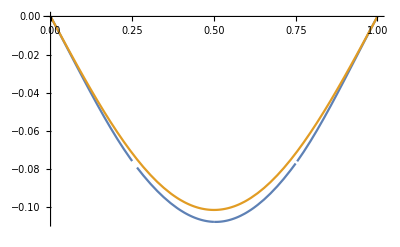

```mathematica
coeff=coeff/.h->hx/.Subscript[g0, 1]->g0Tbl[[1]]/.Subscript[g0, 2]->g0Tbl[[2]]/.Subscript[g0, 3]->g0Tbl[[3]]/.Subscript[g0, 4]->g0Tbl[[4]]/.Subscript[g0, 5]->g0Tbl[[5]]/.Subscript[g1, 1]->g1Tbl[[1]]/.Subscript[g1, 2]->g1Tbl[[2]]/.Subscript[g1, 3]->g0Tbl[[3]]/.Subscript[g1, 4]->g1Tbl[[4]]/.Subscript[g1, 5]->g1Tbl[[5]]/.Subscript[f0, 1]->yaTbl[[1]]/.Subscript[f1, 1]->d1yaTbl[[1]]/.Subscript[f0, 5]->yaTbl[[5]]/.Subscript[f1, 5]->d1yaTbl[[5]]

coeff0=coeff[[1;;6;;2]];
coeff0=PrependTo[coeff0,yaTbl[[1]]];
coeff0=AppendTo[coeff0,yaTbl[[5]]]
coeff1=coeff[[2;;6;;2]];
coeff1=PrependTo[coeff1,d1yaTbl[[1]]]
coeff1=AppendTo[coeff1,d1yaTbl[[5]]];
		
ϕ00=BasisCIPBS[x,0,1][[3]]/.h->hx;
ϕ01=BasisCIPBS[x,1,1][[3]]/.h->hx;

fApprox=Sum[(coeff0[[k]]ϕ00/.x->x-xTbl[[k]]//Simplify)+(coeff1[[k]]ϕ01/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify

Plot[{fApprox,ya[x]},{x,a-0hx,b+0hx}]
```

```mathematica
coeff
coeff0
coeff1
d1yaTbl
```

{-0.0757912,-0.233882,-0.107567,-0.00592758,-0.0769223,0.235749}

{0.,-0.0757912,-0.107567,-0.0769223,-1.24083×10^-17}

{-0.31831,-0.233882,-0.00592758,0.235749,0.31831}

{-0.31831,-0.225079,-1.94909×10^-17,0.225079,0.31831}

```mathematica
t0=Table[(coeff0[[k]]ϕ00/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}];
t1=Table[(coeff1[[k]]ϕ01/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}];
```

```mathematica
t1//Total
```

(Piecewise[{{0., x>0.5||x<0}, {0.233882-1.87106 x+4.67764 x^2-3.74212 x^3, 0.25<x≤0.5}, {(0.935529-3.74212 x) x^2, True}}])+(Piecewise[{{0., x>0.75||x<0.25}, {0.0266741-0.124479 x+0.189683 x^2-0.0948413 x^3, 0.5<x≤0.75}, {0.00296379-0.0296379 x+0.0948413 x^2-0.0948413 x^3, True}}])+(Piecewise[{{0., x>1.||x<0.5}, {-2.82898+9.42994 x-10.3729 x^2+3.77198 x^3, 0.75<x≤1.}, {-0.707246+3.77198 x-6.60096 x^2+3.77198 x^3, True}}])+(Piecewise[{{0., x>1.25||x<0.75}, {-7.95775+20.6901 x-17.8254 x^2+5.09296 x^3, 1.<x≤1.25}, {-2.86479+10.5042 x-12.7324 x^2+5.09296 x^3, True}}])-0.31831 (Piecewise[{{(1-4 x)^2 x, 0<x≤0.25}, {x (1+4 x)^2, -0.25≤x≤0}, {0, True}}])

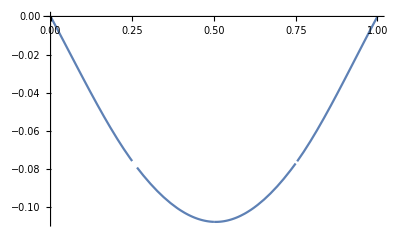

```mathematica
Plot[{(t0+t1)//Total},{x,a-0hx,b+0hx},PlotRange->All]
```